```mathematica
description="Leading order cross section of slepton pair production.";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
MakeBoxes[p1, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(1\)]\)";
MakeBoxes[p2, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(2\)]\)";
MakeBoxes[k1, TraditionalForm] := "\!\(\*SubscriptBox[\(k\),\(1\)]\)"; 
MakeBoxes[k2, TraditionalForm] := "\!\(\*SubscriptBox[\(k\),\(2\)]\)";
```

## LO diagrams to combine for interference terms

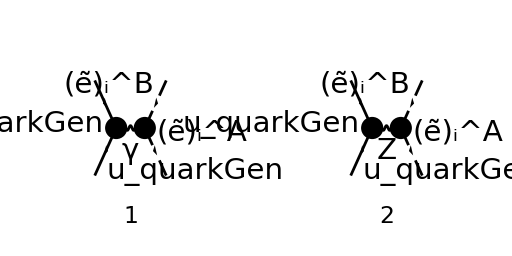

```mathematica
diagsLO=InsertFields[
CreateTopologies[0,2->2],{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{S[1],S[2],S[3],S[4]}
];
Paint[
diagsLO,
ColumnsXRows->{2,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

```mathematica
MLO[0]=FCFAConvert[
CreateFeynAmp[diagsLO],(*Create amplitudes in FeynArts*)
IncomingMomenta->{p1,p2},(*Define incoming momenta*)
OutgoingMomenta->{k1,k2},(*Define outgoing momenta*)
ChangeDimension->D,(*Define spacetime dimension*)
UndoChiralSplittings->True,(*No left/right-splitting in Mγ*)
List->False,(*Output the amplitude alone, not in a list*)
Contract->True,(*Replace  with *)
DropSumOver->True,(*SumOver from FeynArts is dropped. Einstein summation applies, so it is not needed.*)
SMP->True (*Use SMP for parameters (e.g. SMP["m_e"] = electron mass)*)
]/.{MQU[quarkGen]->0}
```

(2 e^2 δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(k_1-k_2)).(φ(p_1)))/(3 (k_1+k_2)^2)-(ⅈ e (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-p_2)).((2 ⅈ e δ_Col1Col2 (sin(θ_W)) (γ·(k_1-k_2)).(γ̄)^6)/(3 (cos(θ_W)))+(ⅈ e δ_Col1Col2 (4 (sin(θ_W))^2-3) (γ·(k_1-k_2)).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/(2 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2))

Change  to for quark charge in photon diagram.

```mathematica
MγLO[0]=Part[MLO[0],1] 3/2 SMP["e_Q"];
MZLO[0]=Part[MLO[0],2];
MLO[1]=MγLO[0]+MZLO[0]
```

(e^2 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(k_1-k_2)).(φ(p_1)))/(k_1+k_2)^2-(ⅈ e (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-p_2)).((2 ⅈ e δ_Col1Col2 (sin(θ_W)) (γ·(k_1-k_2)).(γ̄)^6)/(3 (cos(θ_W)))+(ⅈ e δ_Col1Col2 (4 (sin(θ_W))^2-3) (γ·(k_1-k_2)).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/(2 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2))

```mathematica
MLO[2]=MLO[1]/.{4 SMP["sin_W"]^2-3:>12 Zql};
MLO[3]=MLO[2]/.{SMP["sin_W"]/SMP["cos_W"]:>3 Zqr / (SMP["sin_W"] SMP["cos_W"])}
```

(e^2 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(k_1-k_2)).(φ(p_1)))/(k_1+k_2)^2-(ⅈ e (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-p_2)).((2 ⅈ e Zql δ_Col1Col2 (γ·(k_1-k_2)).(γ̄)^7)/((cos(θ_W)) (sin(θ_W)))+(2 ⅈ e Zqr δ_Col1Col2 (γ·(k_1-k_2)).(γ̄)^6)/((cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/(2 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2))

```mathematica
MLO[4]=MLO[3]//.{USf[2,i][A,2] Conjugate[USf[2,i][B,2]]:>KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]}//Simplify
```

(e^2 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(k_1-k_2)).(φ(p_1)))/(k_1+k_2)^2-(ⅈ e (2 (sin(θ_W))^2 A,B-USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(k_1-k_2)).(γ̄)^7+Zqr (γ·(k_1-k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/(2 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2))

```mathematica
MLO[5]=MLO[4]//.{2SMP["sin_W"]^2 KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]->-2 ZliAB}
```

(e^2 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(k_1-k_2)).(φ(p_1)))/(k_1+k_2)^2+(ⅈ e ZliAB (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(k_1-k_2)).(γ̄)^7+Zqr (γ·(k_1-k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2))

## Full diagrams with slepton self-energies

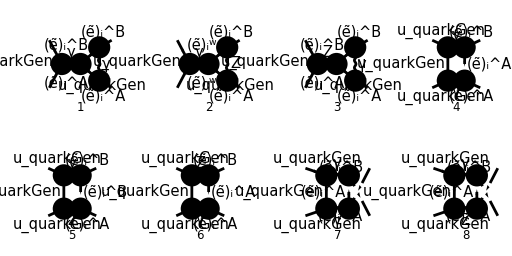

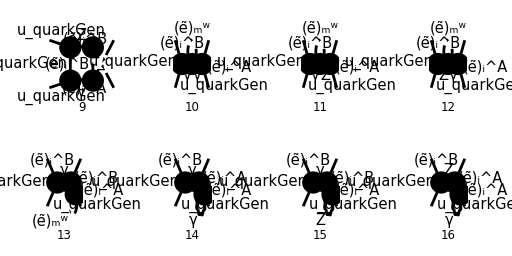

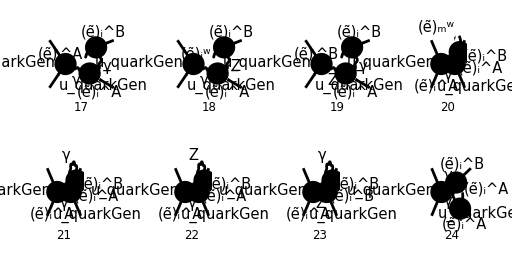

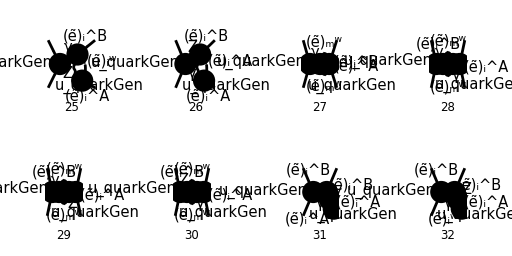

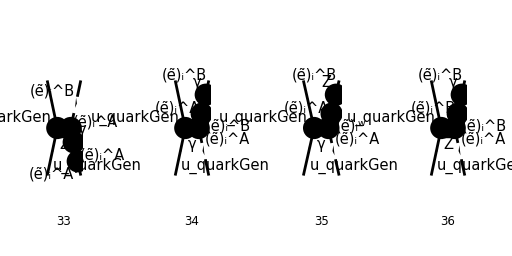

```mathematica
diagsFull[0]=InsertFields[
CreateTopologies[1,2->2,ExcludeTopologies->{Tadpoles}],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{S[1],S[2],S[3],S[4],S[5],S[6],V[3],F[11],F[12],S[13],S[14],S[11]},
LastSelections->{V[1],S[12]}
];
Paint[
diagsFull[0],
ColumnsXRows->{4,2},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

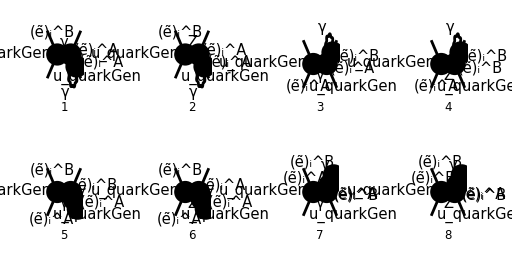

```mathematica
diagsFull[1]=DiagramExtract[diagsFull[0],{14,16,21,23,31,33,34,36}];
Paint[
diagsFull[1],
ColumnsXRows->{4,2},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

```mathematica
Mlist[0]=FCFAConvert[
CreateFeynAmp[diagsFull[1]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k2},
LoopMomenta->{kloop},
ChangeDimension->D,
UndoChiralSplittings->True,
Contract->True,
DropSumOver->True,
SMP->True,
List->True
]/.{MQU[quarkGen]->0}
```

{-(ⅈ D (φ(-p_2)).(γ·(k_2-k_1)).(φ(p_1)) IndexDelta(A,B) e^4 δ_Col1Col2)/(24 π^4 (k_1+k_2)^2 kloop^2 (k_2^2-(MSf(A,2,i))^2)),-((D (φ(-p_2)).((2 ⅈ (γ·(k_2-k_1)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ·(k_2-k_1)).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) e^3 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(32 π^4 kloop^2 (k_2^2-(MSf(A,2,i))^2) ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))),(ⅈ D (φ(-p_2)).(γ·(k_1-k_2)).(φ(p_1)) IndexDelta(A,B) e^4 δ_Col1Col2)/(24 π^4 (k_1+k_2)^2 kloop^2 (k_1^2-(MSf(A,2,i))^2)),(D (φ(-p_2)).((2 ⅈ (γ·(k_1-k_2)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ·(k_1-k_2)).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) e^3 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(32 π^4 kloop^2 (k_1^2-(MSf(B,2,i))^2) ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W))),-(ⅈ (φ(-p_2)).(γ·(k_2-k_1)).(φ(p_1)) IndexDelta(A,B) (-k_2^2+2 (k_2·kloop)-kloop^2) e^4 δ_Col1Col2)/(24 π^4 (kloop^2-(MSf(A,2,i))^2).(k_2+kloop)^2 (k_1+k_2)^2 (k_2^2-(MSf(B,2,i))^2)),-(((φ(-p_2)).((2 ⅈ (γ·(k_2-k_1)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ·(k_2-k_1)).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) (-k_2^2+2 (k_2·kloop)-kloop^2) e^3 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(32 π^4 (kloop^2-(MSf(A,2,i))^2).(k_2+kloop)^2 (k_2^2-(MSf(A,2,i))^2) ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))),(ⅈ (φ(-p_2)).(γ·(k_1-k_2)).(φ(p_1)) IndexDelta(A,B) (-k_1^2+2 (k_1·kloop)-kloop^2) e^4 δ_Col1Col2)/(24 π^4 (kloop^2-(MSf(B,2,i))^2).(k_1+kloop)^2 (k_1+k_2)^2 (k_1^2-(MSf(A,2,i))^2)),((φ(-p_2)).((2 ⅈ (γ·(k_1-k_2)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ·(k_1-k_2)).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) (-k_1^2+2 (k_1·kloop)-kloop^2) e^3 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(32 π^4 (kloop^2-(MSf(B,2,i))^2).(k_1+kloop)^2 (k_1^2-(MSf(B,2,i))^2) ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))}

### Check that the “flower”-diagrams still give zero

```mathematica
Mflower[0]=Total[Mlist[0][[1;;4]]]
```

(D e^3 (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-p_2)).((2 ⅈ e δ_Col1Col2 (sin(θ_W)) (γ·(k_1-k_2)).(γ̄)^6)/(3 (cos(θ_W)))+(ⅈ e δ_Col1Col2 (4 (sin(θ_W))^2-3) (γ·(k_1-k_2)).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/(32 π^4 kloop^2 (cos(θ_W)) (sin(θ_W)) (k_1^2-(MSf(B,2,i))^2) ((k_1+k_2)^2-m_Z^2))-(D e^3 (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-p_2)).((2 ⅈ e δ_Col1Col2 (sin(θ_W)) (γ·(k_2-k_1)).(γ̄)^6)/(3 (cos(θ_W)))+(ⅈ e δ_Col1Col2 (4 (sin(θ_W))^2-3) (γ·(k_2-k_1)).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/(32 π^4 kloop^2 (cos(θ_W)) (sin(θ_W)) (k_2^2-(MSf(A,2,i))^2) ((k_1+k_2)^2-m_Z^2))+(ⅈ D e^4 δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(k_1-k_2)).(φ(p_1)))/(24 π^4 kloop^2 (k_1+k_2)^2 (k_1^2-(MSf(A,2,i))^2))-(ⅈ D e^4 δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(k_2-k_1)).(φ(p_1)))/(24 π^4 kloop^2 (k_1+k_2)^2 (k_2^2-(MSf(A,2,i))^2))

```mathematica
Mflower[1]=Mflower[0]//TID[#,kloop,ToPaVe->True]&
```

0

### Do the bubble diagrams

Change  to for quark charge in photon diagram.

```mathematica
Mbubbleγ[0]=Total[Mlist[0][[{5,7}]]] 3/2 SMP["e_Q"]//Simplify
```

-1/(16 π^4 (k_1+k_2)^2)ⅈ e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (((-2 (k_1·kloop)+kloop^2+k_1^2) (φ(-p_2)).(γ·(k_1-k_2)).(φ(p_1)))/((k_1^2-(MSf(A,2,i))^2) (kloop^2-(MSf(B,2,i))^2).(k_1+kloop)^2)-((-2 (k_2·kloop)+kloop^2+k_2^2) (φ(-p_2)).(γ·(k_2-k_1)).(φ(p_1)))/((k_2^2-(MSf(B,2,i))^2) (kloop^2-(MSf(A,2,i))^2).(k_2+kloop)^2))

#### SJEKK AT DETTE BLE RIKTIG:

```mathematica
Mbubbleγ[1]=Mbubbleγ[0]/.{
FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],MSf[A,2,i]]]->FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],MSf[B,2,i]]],
FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],MSf[B,2,i]]]->FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],MSf[A,2,i]]]
}
```

-1/(16 π^4 (k_1+k_2)^2)ⅈ e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (((-2 (k_1·kloop)+kloop^2+k_1^2) (φ(-p_2)).(γ·(k_1-k_2)).(φ(p_1)))/((k_1^2-(MSf(B,2,i))^2) (kloop^2-(MSf(B,2,i))^2).(k_1+kloop)^2)-((-2 (k_2·kloop)+kloop^2+k_2^2) (φ(-p_2)).(γ·(k_2-k_1)).(φ(p_1)))/((k_2^2-(MSf(A,2,i))^2) (kloop^2-(MSf(A,2,i))^2).(k_2+kloop)^2))

The Z-propagator part

```mathematica
MbubbleZ[0]=Total[Mlist[0][[{6,8}]]];
MbubbleZ[1]=MbubbleZ[0]/.{4 SMP["sin_W"]^2-3:>12 Zql};
MbubbleZ[2]=MbubbleZ[1]/.{SMP["sin_W"]/SMP["cos_W"]:>3 Zqr / (SMP["sin_W"] SMP["cos_W"])};
MbubbleZ[3]=MbubbleZ[2]//.{USf[2,i][A,2] Conjugate[USf[2,i][B,2]]:>KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]}//Simplify;
MbubbleZ[4]=MbubbleZ[3]//.{2SMP["sin_W"]^2 KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]->-2 ZliAB}
```

-((e^3 ZliAB (((-2 (k_2·kloop)+kloop^2+k_2^2) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(k_2-k_1)).(γ̄)^7+Zqr (γ·(k_2-k_1)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((k_2^2-(MSf(A,2,i))^2) (kloop^2-(MSf(A,2,i))^2).(k_2+kloop)^2)-((-2 (k_1·kloop)+kloop^2+k_1^2) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(k_1-k_2)).(γ̄)^7+Zqr (γ·(k_1-k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((k_1^2-(MSf(B,2,i))^2) (kloop^2-(MSf(B,2,i))^2).(k_1+kloop)^2)))/(16 π^4 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2)))

Combining the diagrams (and substituting kloop -> -kloop to get the same convention as the hand calculation. This is allowed since we integrate over all k

```mathematica
Mbubble[0]=Mbubbleγ[0]+MbubbleZ[4]/.{kloop->-kloop}
```

-1/(16 π^4 (k_1+k_2)^2)ⅈ e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (((2 (k_1·kloop)+kloop^2+k_1^2) (φ(-p_2)).(γ·(k_1-k_2)).(φ(p_1)))/((k_1^2-(MSf(A,2,i))^2) (kloop^2-(MSf(B,2,i))^2).(k_1-kloop)^2)-((2 (k_2·kloop)+kloop^2+k_2^2) (φ(-p_2)).(γ·(k_2-k_1)).(φ(p_1)))/((k_2^2-(MSf(B,2,i))^2) (kloop^2-(MSf(A,2,i))^2).(k_2-kloop)^2))-(e^3 ZliAB (((2 (k_2·kloop)+kloop^2+k_2^2) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(k_2-k_1)).(γ̄)^7+Zqr (γ·(k_2-k_1)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((k_2^2-(MSf(A,2,i))^2) (kloop^2-(MSf(A,2,i))^2).(k_2-kloop)^2)-((2 (k_1·kloop)+kloop^2+k_1^2) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(k_1-k_2)).(γ̄)^7+Zqr (γ·(k_1-k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((k_1^2-(MSf(B,2,i))^2) (kloop^2-(MSf(B,2,i))^2).(k_1-kloop)^2)))/(16 π^4 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2))

```mathematica
Mbubble[1]=Mbubble[0]//TID[#,kloop,ToPaVe->True]&//Simplify
```

(e^4 (A_0((MSf(B,2,i))^2) (-((φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (cos(θ_W))^2 e_Q (sin(θ_W))^2)/((k_1^2-(MSf(A,2,i))^2).(k_1+k_2)^2)+((φ(-p_2)).(γ·k_2).(φ(p_1)) IndexDelta(A,B) (cos(θ_W))^2 e_Q (sin(θ_W))^2)/((k_1^2-(MSf(A,2,i))^2).(k_1+k_2)^2)+(2 ZliAB Zqr (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)))/((k_1^2-(MSf(B,2,i))^2).((k_1+k_2)^2-m_Z^2))+(2 ZliAB Zql (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)))/((k_1^2-(MSf(B,2,i))^2).((k_1+k_2)^2-m_Z^2))-(2 ZliAB Zqr (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)))/((k_1^2-(MSf(B,2,i))^2).((k_1+k_2)^2-m_Z^2))-(2 ZliAB Zql (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)))/((k_1^2-(MSf(B,2,i))^2).((k_1+k_2)^2-m_Z^2)))+A_0((MSf(A,2,i))^2) (-((φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (cos(θ_W))^2 e_Q (sin(θ_W))^2)/((k_2^2-(MSf(B,2,i))^2).(k_1+k_2)^2)+((φ(-p_2)).(γ·k_2).(φ(p_1)) IndexDelta(A,B) (cos(θ_W))^2 e_Q (sin(θ_W))^2)/((k_2^2-(MSf(B,2,i))^2).(k_1+k_2)^2)+(2 ZliAB Zqr (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)))/((k_2^2-(MSf(A,2,i))^2).((k_1+k_2)^2-m_Z^2))+(2 ZliAB Zql (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)))/((k_2^2-(MSf(A,2,i))^2).((k_1+k_2)^2-m_Z^2))-(2 ZliAB Zqr (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)))/((k_2^2-(MSf(A,2,i))^2).((k_1+k_2)^2-m_Z^2))-(2 ZliAB Zql (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)))/((k_2^2-(MSf(A,2,i))^2).((k_1+k_2)^2-m_Z^2)))-2 (B_0(k_1^2,0,(MSf(B,2,i))^2) ((MSf(B,2,i))^2+k_1^2) (-((φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (cos(θ_W))^2 e_Q (sin(θ_W))^2)/((k_1^2-(MSf(A,2,i))^2).(k_1+k_2)^2)+((φ(-p_2)).(γ·k_2).(φ(p_1)) IndexDelta(A,B) (cos(θ_W))^2 e_Q (sin(θ_W))^2)/((k_1^2-(MSf(A,2,i))^2).(k_1+k_2)^2)+(2 ZliAB Zqr (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)))/((k_1^2-(MSf(B,2,i))^2).((k_1+k_2)^2-m_Z^2))+(2 ZliAB Zql (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)))/((k_1^2-(MSf(B,2,i))^2).((k_1+k_2)^2-m_Z^2))-(2 ZliAB Zqr (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)))/((k_1^2-(MSf(B,2,i))^2).((k_1+k_2)^2-m_Z^2))-(2 ZliAB Zql (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)))/((k_1^2-(MSf(B,2,i))^2).((k_1+k_2)^2-m_Z^2)))+B_0(k_2^2,0,(MSf(A,2,i))^2) ((MSf(A,2,i))^2+k_2^2) (-((φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (cos(θ_W))^2 e_Q (sin(θ_W))^2)/((k_2^2-(MSf(B,2,i))^2).(k_1+k_2)^2)+((φ(-p_2)).(γ·k_2).(φ(p_1)) IndexDelta(A,B) (cos(θ_W))^2 e_Q (sin(θ_W))^2)/((k_2^2-(MSf(B,2,i))^2).(k_1+k_2)^2)+(2 ZliAB Zqr (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)))/((k_2^2-(MSf(A,2,i))^2).((k_1+k_2)^2-m_Z^2))+(2 ZliAB Zql (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)))/((k_2^2-(MSf(A,2,i))^2).((k_1+k_2)^2-m_Z^2))-(2 ZliAB Zqr (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)))/((k_2^2-(MSf(A,2,i))^2).((k_1+k_2)^2-m_Z^2))-(2 ZliAB Zql (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)))/((k_2^2-(MSf(A,2,i))^2).((k_1+k_2)^2-m_Z^2))))) δ_Col1Col2)/(16 π^2 (cos(θ_W))^2 (sin(θ_W))^2)

```mathematica
Mbubble[2]=Mbubble[1]//FeynAmpDenominatorExplicit//Simplify
```

(e^4 (A_0((MSf(B,2,i))^2) (((φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (cos(θ_W))^2 e_Q (sin(θ_W))^2)/(((MSf(A,2,i))^2-k_1^2) (k_1^2+2 (k_1·k_2)+k_2^2))+((φ(-p_2)).(γ·k_2).(φ(p_1)) IndexDelta(A,B) (cos(θ_W))^2 e_Q (sin(θ_W))^2)/((k_1^2-(MSf(A,2,i))^2) (k_1^2+2 (k_1·k_2)+k_2^2))+(2 ZliAB Zqr (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)))/(((MSf(B,2,i))^2-k_1^2) (-m_Z^2+k_1^2+2 (k_1·k_2)+k_2^2))+(2 ZliAB Zql (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)))/(((MSf(B,2,i))^2-k_1^2) (-m_Z^2+k_1^2+2 (k_1·k_2)+k_2^2))+(2 ZliAB Zqr (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)))/((k_1^2-(MSf(B,2,i))^2) (-m_Z^2+k_1^2+2 (k_1·k_2)+k_2^2))+(2 ZliAB Zql (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)))/((k_1^2-(MSf(B,2,i))^2) (-m_Z^2+k_1^2+2 (k_1·k_2)+k_2^2)))+A_0((MSf(A,2,i))^2) (((φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (cos(θ_W))^2 e_Q (sin(θ_W))^2)/(((MSf(B,2,i))^2-k_2^2) (k_1^2+2 (k_1·k_2)+k_2^2))+((φ(-p_2)).(γ·k_2).(φ(p_1)) IndexDelta(A,B) (cos(θ_W))^2 e_Q (sin(θ_W))^2)/((k_2^2-(MSf(B,2,i))^2) (k_1^2+2 (k_1·k_2)+k_2^2))+(2 ZliAB Zqr (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)))/(((MSf(A,2,i))^2-k_2^2) (-m_Z^2+k_1^2+2 (k_1·k_2)+k_2^2))+(2 ZliAB Zql (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)))/(((MSf(A,2,i))^2-k_2^2) (-m_Z^2+k_1^2+2 (k_1·k_2)+k_2^2))+(2 ZliAB Zqr (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)))/((k_2^2-(MSf(A,2,i))^2) (-m_Z^2+k_1^2+2 (k_1·k_2)+k_2^2))+(2 ZliAB Zql (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)))/((k_2^2-(MSf(A,2,i))^2) (-m_Z^2+k_1^2+2 (k_1·k_2)+k_2^2)))-2 (B_0(k_1^2,0,(MSf(B,2,i))^2) ((MSf(B,2,i))^2+k_1^2) (((φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (cos(θ_W))^2 e_Q (sin(θ_W))^2)/(((MSf(A,2,i))^2-k_1^2) (k_1^2+2 (k_1·k_2)+k_2^2))+((φ(-p_2)).(γ·k_2).(φ(p_1)) IndexDelta(A,B) (cos(θ_W))^2 e_Q (sin(θ_W))^2)/((k_1^2-(MSf(A,2,i))^2) (k_1^2+2 (k_1·k_2)+k_2^2))+(2 ZliAB Zqr (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)))/(((MSf(B,2,i))^2-k_1^2) (-m_Z^2+k_1^2+2 (k_1·k_2)+k_2^2))+(2 ZliAB Zql (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)))/(((MSf(B,2,i))^2-k_1^2) (-m_Z^2+k_1^2+2 (k_1·k_2)+k_2^2))+(2 ZliAB Zqr (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)))/((k_1^2-(MSf(B,2,i))^2) (-m_Z^2+k_1^2+2 (k_1·k_2)+k_2^2))+(2 ZliAB Zql (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)))/((k_1^2-(MSf(B,2,i))^2) (-m_Z^2+k_1^2+2 (k_1·k_2)+k_2^2)))+B_0(k_2^2,0,(MSf(A,2,i))^2) ((MSf(A,2,i))^2+k_2^2) (((φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (cos(θ_W))^2 e_Q (sin(θ_W))^2)/(((MSf(B,2,i))^2-k_2^2) (k_1^2+2 (k_1·k_2)+k_2^2))+((φ(-p_2)).(γ·k_2).(φ(p_1)) IndexDelta(A,B) (cos(θ_W))^2 e_Q (sin(θ_W))^2)/((k_2^2-(MSf(B,2,i))^2) (k_1^2+2 (k_1·k_2)+k_2^2))+(2 ZliAB Zqr (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)))/(((MSf(A,2,i))^2-k_2^2) (-m_Z^2+k_1^2+2 (k_1·k_2)+k_2^2))+(2 ZliAB Zql (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)))/(((MSf(A,2,i))^2-k_2^2) (-m_Z^2+k_1^2+2 (k_1·k_2)+k_2^2))+(2 ZliAB Zqr (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)))/((k_2^2-(MSf(A,2,i))^2) (-m_Z^2+k_1^2+2 (k_1·k_2)+k_2^2))+(2 ZliAB Zql (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)))/((k_2^2-(MSf(A,2,i))^2) (-m_Z^2+k_1^2+2 (k_1·k_2)+k_2^2))))) δ_Col1Col2)/(16 π^2 (cos(θ_W))^2 (sin(θ_W))^2)

### Retrieve LO amp

```mathematica
(*MLO[0]=Import[FileNameJoin[{NotebookDirectory[],"results/LOamp.m"}]]//ChangeDimension[#,D]&*)
```

```mathematica
MLOCC[0]=ComplexConjugate[MLO[5]]
```

(e^2 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(p_1)).(γ·(k_1-k_2)).(φ(-p_2)))/(k_1+k_2)^2-(2 e^2 ZliAB δ_Col1Col2 (φ(p_1)).(Zql (γ̄)^6.(γ·(k_1-k_2))+Zqr (γ̄)^7.(γ·(k_1-k_2))).(φ(-p_2)))/((cos(θ_W))^2 (sin(θ_W))^2 ((k_1+k_2)^2-m_Z^2))

```mathematica
Minterference[0]=Mbubble[2] MLOCC[0]//DiracSimplify//Simplify
```

(e^6 (-(2 10 (1)^4)/(1)^2+1/1^2+644+1/1) δ_Col1Col2^2)/(16 π^2 7 (sin(θ_W))^4)
 |  |  |  |

### Compare to hand calculation

Note: Have so far computed MM*, not 2Re(MM*), so must also compare with the hand calculation before doing 2Re(...)

```mathematica
MinterferenceHand[0]=-SMP["e"]^2/(16Pi^2) FAD[{k2,MSf[A,2,i]}] (A0[MSf[A,2,i]^2]-2(SPD[k2]+MSf[A,2,i]^2)B0[SPD[k2],0,MSf[A,2,i]^2])+FAD[{k1,MSf[B,2,i]}](A0[MSf[B,2,i]^2]-2(SPD[k1]+MSf[B,2,i]^2)B0[SPD[k1],0,MSf[B,2,i]^2]) MLO[5] MLOCC[0]
```

-(e^2 (A_0((MSf(A,2,i))^2)-2 ((MSf(A,2,i))^2+k_2^2) B_0(k_2^2,0,(MSf(A,2,i))^2)))/(16 π^2 (k_2^2-(MSf(A,2,i))^2))+1/(k_1^2-(MSf(B,2,i))^2)(A_0((MSf(B,2,i))^2)-2 ((MSf(B,2,i))^2+k_1^2) B_0(k_1^2,0,(MSf(B,2,i))^2)) ((e^2 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(k_1-k_2)).(φ(p_1)))/(k_1+k_2)^2+(ⅈ e ZliAB (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(k_1-k_2)).(γ̄)^7+Zqr (γ·(k_1-k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2))) ((e^2 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(p_1)).(γ·(k_1-k_2)).(φ(-p_2)))/(k_1+k_2)^2-(2 e^2 ZliAB δ_Col1Col2 (φ(p_1)).(Zql (γ̄)^6.(γ·(k_1-k_2))+Zqr (γ̄)^7.(γ·(k_1-k_2))).(φ(-p_2)))/((cos(θ_W))^2 (sin(θ_W))^2 ((k_1+k_2)^2-m_Z^2)))

```mathematica
FCCompareResults[{Minterference[0]},{MinterferenceHand[0]},Text->{"Compare to hand calculations:","Correct!","Wrong!"},Interrupt->{Hold[Quit[1]],Automatic}];
```

Compare to hand calculations: Wrong!

```mathematica
MinterferenceHand[0]
```

-(e^2 (A_0((MSf(A,2,i))^2)-2 ((MSf(A,2,i))^2+k_2^2) B_0(k_2^2,0,(MSf(A,2,i))^2)))/(16 π^2 (k_2^2-(MSf(A,2,i))^2))+1/(k_1^2-(MSf(B,2,i))^2)(A_0((MSf(B,2,i))^2)-2 ((MSf(B,2,i))^2+k_1^2) B_0(k_1^2,0,(MSf(B,2,i))^2)) ((e^2 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(k_1-k_2)).(φ(p_1)))/(k_1+k_2)^2+(ⅈ e ZliAB (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(k_1-k_2)).(γ̄)^7+Zqr (γ·(k_1-k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2))) ((e^2 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(p_1)).(γ·(k_1-k_2)).(φ(-p_2)))/(k_1+k_2)^2-(2 e^2 ZliAB δ_Col1Col2 (φ(p_1)).(Zql (γ̄)^6.(γ·(k_1-k_2))+Zqr (γ̄)^7.(γ·(k_1-k_2))).(φ(-p_2)))/((cos(θ_W))^2 (sin(θ_W))^2 ((k_1+k_2)^2-m_Z^2)))

```mathematica
Minterference[0]//DiracSimplify//Simplify
```

(e^6 (-(2 10 (1)^4)/(1)^2+1/1^2+644+1/1) δ_Col1Col2^2)/(16 π^2 7 (sin(θ_W))^4)
 |  |  |  |